# Лабораторная работа №5

## Грицак Александра, гр.ПО-4

Задание 1.
Подберите примеры, подтверждающие справедливость следующих утверждений:

а) пробел выполняет роль знака умножения

```mathematica
3 18
```

54

б) введение дополнительных пробелов не изменяет результата вычислений

```mathematica
3   18
```

54

```mathematica
3+       18
```

21

в) целые, рациональные и иррациональные числа считаются заданными точно (поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя)

```mathematica
4/11
```

4/11

г) действительные числа, содержащие точку, считаются заданными приближенно (поэтому выражения, в которые входят действительные числа,  вычисляются при обработке секции без специальной команды)

```mathematica
4/11.
```

0.363636

д) для изменения стандартного порядка выполнения операций используются кргулые скобки

```mathematica
4+2*2
```

8

```mathematica
(4+2)*2
```

12

Задание 2.

а) с помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр, проверить  точность полученного результата с помощью Precision

```mathematica
N[Sqrt[17],200]
(* дает численный результат с точностью до n цифр *)
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
(*дает эффективное количество цифр точности в числе x.*)
```

200.

б) найти приближенное значение числа с точностью до 40 значащих цифр, вычислить насколько полученный результат отличается от ближайшего к нему целого числа.

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[%]
```

262537412640768744

в) вычислите -Graphics-

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

г) последовательно введите выражение

```mathematica
5>3
```

True

```mathematica
5<2
```

False

-определить справедливо или нет неравенство , найти численные значения левой и правой частей неравенства и убедиться в правильности полученного результата.

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

```mathematica
Pi^E > E^Pi
```

False

Задание 3.

а) решить уравнения -Graphics-

```mathematica
NSolve[Sqrt[x+2]+4*x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3 -3*x^2 + 5 ==0,x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

б) решить системы уравнений:
 -Graphics-

```mathematica
NSolve[{x^2+x*y+y^2==1,x^3+x^2*y+x*y^2+y^3==4},{x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z==34,x+y-z==-1,-x+2*y+3*z==4},{x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

в) придумайте уравнение или систему полиномиальных уравнений и найдите численное решение

```mathematica
NSolve[{(x^2+5*x+10)/(x+1)==0, x^2+y^2==1},{x,y}]
```

{{x→-2.5-1.93649 ⅈ,y→-2.0369+2.37676 ⅈ},{x→-2.5-1.93649 ⅈ,y→2.0369-2.37676 ⅈ},{x→-2.5+1.93649 ⅈ,y→-2.0369-2.37676 ⅈ},{x→-2.5+1.93649 ⅈ,y→2.0369+2.37676 ⅈ}}

Задание 4.

Используя функцию FindRoot, найти решения следующего уравнения (вариант7)
-Graphics-

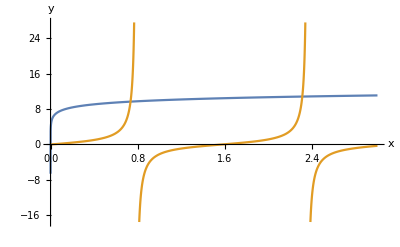

```mathematica
Plot[{Log[x]+10,Tan[2*x]},{x,0,3},AxesLabel->{"x","y"}]
(*посторим графики левой и правой части уравнения*)
```

```mathematica
x1 = 0.7;x2 = 2.3;
(*на графике мы видим два корня(точки пересечения кривых), из грвфика находим приближенные значения корней*)
```

```mathematica
FindRoot[Log[x]+10==Tan[2*x],{x,x1}]
(*находим точные значения с помощью FindRoot(ищет числовой корень функции, начиная с точки x = x0)*)
```

{x→0.733984}

```mathematica
FindRoot[Log[x]+10==Tan[2*x],{x,x2}]
```

{x→2.31019}

Задание 5.

Найти решение дифференциального уравнения на заданном отрезке:
-Graphics-
-Graphics-

```mathematica
ol1=NDSolve[{y''[x]+3*x^2*y'[x]- 6*Cos[2*x]*y[x]^2==0, y[0]==-4, y'[0]==3},y, {x,0,5}]
(*найдем решение диф. уравнения с начальными условаиями на отрезке*)
```

{{y→InterpolatingFunction[…]}}

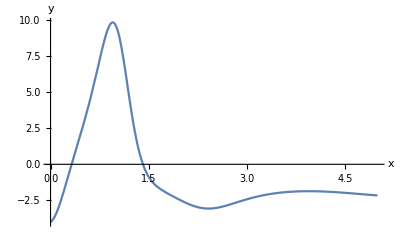

```mathematica
Plot[y[x]/. ol1,{x,0,5}, AxesLabel->{"x","y"}]
(*посторим график уравнения чтобы найти корни найденной функции*)
```

Из графика видим, что на отрезке [0,2] есть два корня уравнения y(x) = 0, которые имеют приближенные значения x1= 0.3 и x2 = 1.4

```mathematica
sol2 = FindRoot[(y[x]/. ol1[[1]])==0,{x,0.3}]
(*находим точные значения корней*)
```

{x→0.322768}

```mathematica
sol3 = FindRoot[(y[x]/. ol1[[1]])==0,{x,1.4}]
```

{x→1.41351}

```mathematica
D[y[x]/.ol1[[1]],x]/.sol2
(*вычисляем значение производной в найденных точках*)
```

15.5257

```mathematica
D[y[x]/.ol1[[1]],x]/.sol3
```

-12.7737

```mathematica
sol4 = FindRoot[D[y[x]/.ol1[[1]],x]==0,{x,2.2}]
(*найденная функция имеет около точки 2.2 локальный миниум, приравниявая производную функции к нулю и решая полученнок уравнение, получим точное значения х*)
```

{x→2.41703}

```mathematica
y[x]/.ol1[[1]]/.sol4
(*находим соотв. значение функции в этой точке*)
```

-3.06756

```mathematica
FindMinimum[y[x]/.ol1[[1]],{x,2.2}]
(*минимальное значение функции в окрестности точки х = 2.2*)
```

{-3.06756,{x→2.41703}}

Задание 6.
а) задать произвольные численные значения параметров a,b,c,d,e в следующих зависимостях:
-Graphics-
Используя функцию Table, поределить список численных данных.
С помощью функции Random внести в каждой точке x случайное значение △y

```mathematica
dat1 = Table[{x, (2+3*x+6*x^2+7*x^3+9*x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,10,0.5}]
(*вычислим значения функции, задавая значения х из интервала [0,10] с шагом 0.5. для каждой точки определим погрешность *)
```

{{0.,1.8191},{0.5,6.78543},{1.,27.9915},{1.5,91.7037},{2.,242.738},{2.5,535.642},{3.,1064.3},{3.5,1843.76},{4.,3113.37},{4.5,4175.81},{5.,7105.9},{5.5,9613.13},{6.,13060.1},{6.5,18497.6},{7.,21986.7},{7.5,32566.},{8.,40351.7},{8.5,47177.1},{9.,59372.4},{9.5,81148.4},{10.,88407.3}}

```mathematica
dat2 = Table[{x, (2+3*x+6*Sin[x]+7*Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,10,0.5}]
```

{{0.,9.48863},{0.5,13.0762},{1.,13.0737},{1.5,14.2257},{2.,9.49106},{2.5,6.79239},{3.,5.00054},{3.5,3.64686},{4.,4.6185},{4.5,7.54749},{5.,13.9649},{5.5,18.4938},{6.,22.8047},{6.5,28.4178},{7.,30.7383},{7.5,35.422},{8.,30.8469},{8.5,26.8244},{9.,25.8396},{9.5,23.0799},{10.,22.5402}}

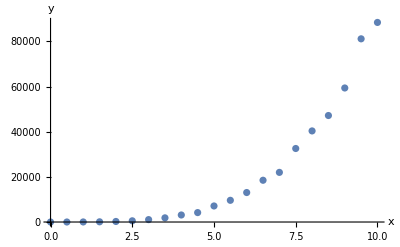

```mathematica
p1 = ListPlot[dat1,AxesLabel->{"x","y"}]
(*чтобы визуально предстваить зависимость y = y(x) отметим экспеременатльные точки на координатной плоскости*)
```

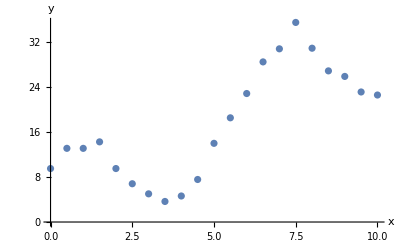

```mathematica
p2 = ListPlot[dat2,AxesLabel->{"x","y"}]
```

```mathematica
y1=Fit[dat1,{1,x,x^2,x^3,x^4},x]
(*чтобы найти наилучшие значения коэфф. в выражении с точки зрения наименьших квадратов*)
(*апроксимация - приближенное представление сложной функции более простой функцией, имеющ. мин. отклонение от исходной функции*)
```

-181.641+582.025 x-317.365 x^2+71.8921 x^3+4.52759 x^4

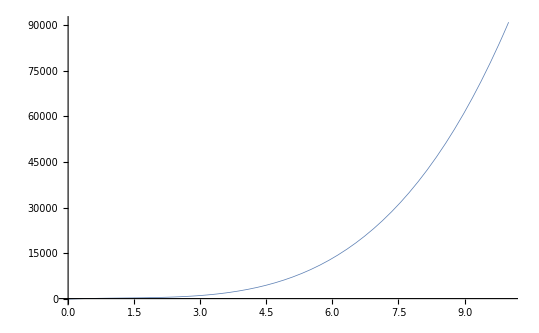

```mathematica
p3 = Plot[y1,{x,0,10},PlotStyle->{{Thickness[0.001]},{Thickness[0.001],Dashing[{0.03}]}}]
```

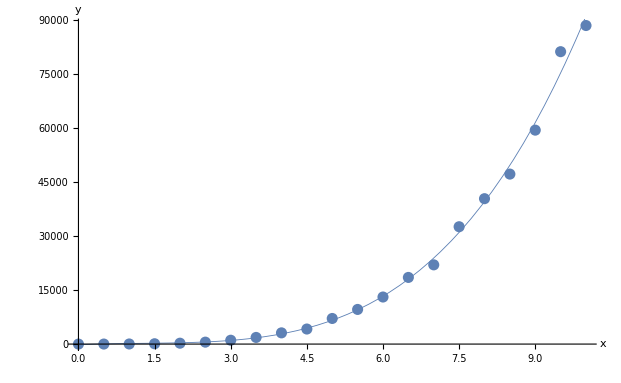

```mathematica
Show[p1,p3]
```

```mathematica
y2=Fit[dat2,{1,x,Sin[x],Cos[x]},x]
```

1.90021+2.97056 x+6.80945 Cos[x]+6.25569 Sin[x]

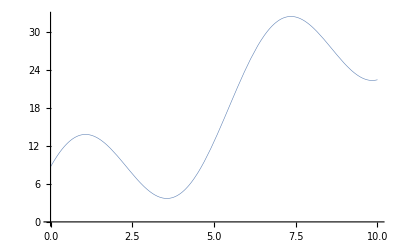

```mathematica
p4 = Plot[y2,{x,0,10},PlotStyle->{{Thickness[0.001]},{Thickness[0.001],Dashing[{0.03}]}}]
```

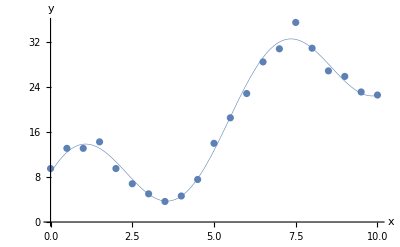

```mathematica
Show[p2,p4]
```